```mathematica
(*2.1*)
a=Sqrt[2.22456/41.498];
k=Sqrt[(33.75242-2.22456)/41.498];
r0=2.1;
A1=Sqrt[(k*a)/(Pi*((2*k*a*r0)-(a*Sin[2*k*r0])+(2*k*Sin[k*r0]^2)))];
c1=A1*Sin[k*r0]*Exp[a*r0];
Plot1=Plot[Piecewise[{{A1*Sin[k*r],0<r<2.09},{c1*Exp[-a*r],2.1<r<5}}],{r,0,5},PlotStyle->Directive[Green, {Thickness[0.005]}],PlotLabels->Placed["2.1fm",{Above}]];
```

```mathematica
(*1.5*)
a=Sqrt[2.22456/41.498];
k2=Sqrt[(59.685237-2.22456)/41.498];
r02=1.5;
A2=Sqrt[(k2*a)/(Pi*((2*k*a*r02)-(a*Sin[2*k2*r02])+(2*k2*Sin[k2*r02]^2)))];
c2=A2*Sin[k2*r02]*Exp[a*r02];
Plot2=Plot[Piecewise[{{A2*Sin[k2*r],0<r<1.49},{c2*Exp[-a*r],1.5<r<5}}],{r,0,5},PlotStyle->Directive[Red, {Thickness[0.005]}],PlotLabels->Placed["1.5fm",{Above}]];
```

```mathematica
(*3*)
alpha=Sqrt[2.22456/41.498];
k3=Sqrt[(19.190514548644952-2.22456)/41.498];
r03=3;
A3=Sqrt[(k3*a)/(Pi*((2*k3*a*r03)-(a*Sin[2*k3*r03])+(2*k3*Sin[k3*r03]^2)))];
c3=A3*Sin[k3*r03]*Exp[a*r03];
Plot3=Plot[Piecewise[{{A3*Sin[k3*r],0<r<3},{c3*Exp[-a*r],3<r<5}}],{r,0,5}, PlotStyle->Directive[Blue, {Thickness[0.005]} ],PlotLabels->Placed["3fm",{Above}]];
```

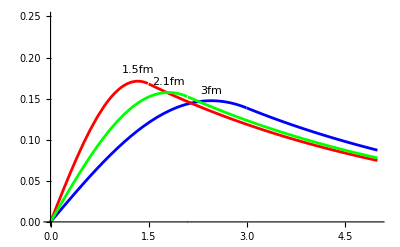

```mathematica
Show[Plot3, Plot2,Plot1,PlotRange->{0,0.25}]
```